```mathematica
basedir="D:\\data\\cycle 195\\exp_CRG-3125\\rawdata\\sc\\"
Get[basedir<>"..\\camera_ifg.m"]
minIntens=2000;  (* Schwellenwert zur Unterdrückung schwach beleuchtetet Randbereiche der Kamera *)
(*
loadimage[basedir<>filename]    liefert Array mit den einzelnen Bildern aus der Tiff-Datei.;
fittile[images_,tileDX_,tileDY_,nx_,ny_,minIntensity_,period_]

*)
```

D:\data\cycle 195\CRG-3125\rawdata\sc\

```mathematica
LoadDatFile[filename_]:=  ToExpression[Transpose[StringSplit[#,"\t"] & /@ Pick[#,StringMatchQ[#,{"\\**","[*"," *","\t*",""}],False]&@Import[basedir<>filename,"lines"]]]
```

```mathematica
reduceSlotsBy[img_,its_,slotmax_]:=Module[{maxph,maxtim},
maxtim=slotmax/its;
maxph=Length[img]/(slotmax+2);
Flatten[Table[    Join[{img[[1+(ph-1)*(slotmax+2)]]},Table[Total[img[[(ph-1)*(slotmax+2)+1+(tim-1)*its;;(ph-1)*(slotmax+2)+tim*its]],1],{tim,1,maxtim}],{img[[ph*(slotmax+2)]]}]     ,{ph,1,maxph}],1]
]
```

```mathematica
(* alle Bilder eines Multi-Page-Images aufsummieren und auf die Anzahl der nicht leeren Pixel normieren *)
integrateImg[img_]:=(Total[#,2]&/@img)   / Count[Flatten[Total[img]],x_/;x>10]
(*integrateImg[img_]:=(Total[#,2]&/@img)   / (Length[img[[1]]]*Length[img[[1,1]]])*)
```

```mathematica
(* counts per pixel *)
cpp[img_]:=N[Total[img,2]  / (Times @@ Dimensions[img])];
```

# Kaiserinterferometer, USANS - Monochromator

```mathematica
filename = "ifg_04Mar0054.tif";
```

{23,64,64}

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

FittedModel::dof: The number of parameters 4 is not less than the number of data values 2. Some property values cannot be computed.

FittedModel::varzero: The estimated variance is zero. Properties requiring division by the variance or standard error will not be computed.

Part::partw: Part 2 of Missing[] does not exist.

Part::partw: Part 2 of If[« 1 »]["ParameterTableEntries"] does not exist.

Part::partd: Part specification « 1 »["ParameterTableEntries"] ⟦ 1, 1 ⟧ is longer than depth of object.

Part::partw: Part 2 of If[« 1 »]["ParameterTableEntries"] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

General::stop: Further output of NonlinearModelFit :: sszero will be suppressed during this calculation.

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of NonlinearModelFit :: cvmit will be suppressed during this calculation.

Part::partd: Part specification « 1 »["ParameterTableEntries"] ⟦ 1, 1 ⟧ is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

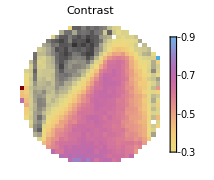
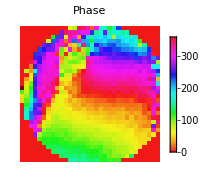
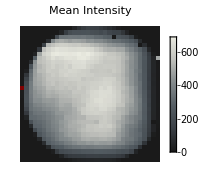
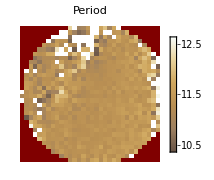

```mathematica
img=loadimage[basedir<>filename]; { Length[img], Length[img[[1]]], Length[img[[1,1]]] }
res=fitgrid[img,2,2,1,11.5];
plotres[res]
```

```mathematica
filename = "ifg_04Mar1804.tif";
```

{23,64,64}

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of NonlinearModelFit :: cvmit will be suppressed during this calculation.

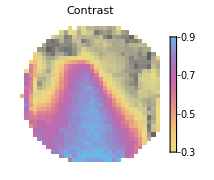
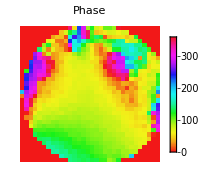
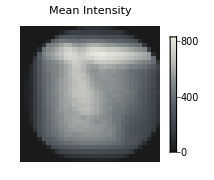
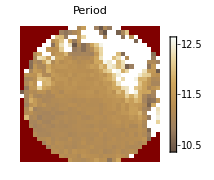

```mathematica
img=loadimage[basedir<>filename]; { Length[img], Length[img[[1]]], Length[img[[1,1]]] }
res=fitgrid[img,2,2,1,11.5];
plotres[res]
```

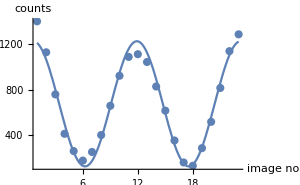
-Graphics- | Estimate | Standard Error | t-Statistic | P-Value
CameraIfgPackage`Private`a | 673.592 | 19.645 | 34.2883 | 1.49365×10^-18
CameraIfgPackage`Private`b | 554.074 | 25.7123 | 21.5489 | 8.17203×10^-15
CameraIfgPackage`Private`c | 0.555342 | 0.00750341 | 74.0119 | 7.4933×10^-25
CameraIfgPackage`Private`d | 1.24565 | 0.0993708 | 12.5353 | 1.2354×10^-10contr=0.822566
offs=673.592
phase=71.3702°
period=11.3141

```mathematica
showtileres[res,14,16]
```

# Standardinterferometer, USANS - Monochromator

```mathematica
spot=loadimage[basedir<>"beamspot.tif"];
spotbox=loadimage[basedir<>"beamspotBoxIn.tif"];
```

```mathematica
{Column[{ArrayPlot[spot[[1]]],ArrayPlot[binimage[spotbox[[1]],2,2]]}],Column[{ArrayPlot[binimage[spotbox[[1]],2,2]],ArrayPlot[spot[[1]]]}]}
```

{-Graphics-
-Graphics-,-Graphics-
-Graphics-}

```mathematica
filename = "ifglong_14Mar1918.tif";
```

{23,64,64}

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

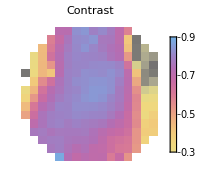
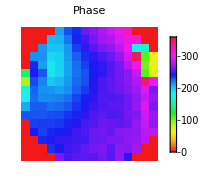
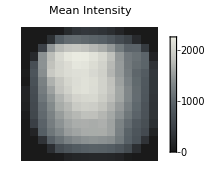
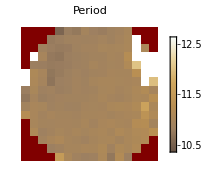

```mathematica
img=loadimage[basedir<>filename]; { Length[img], Length[img[[1]]], Length[img[[1,1]]] }
res=fitgrid[img,4,4,1,11.5];
plotres[res]
```

```mathematica
filename = "ifgPS1_3p_15Mar1918.tif";
```

{35,64,64}

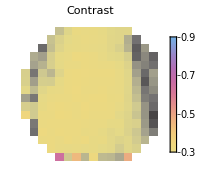
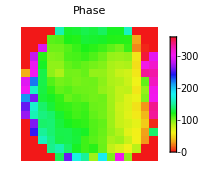
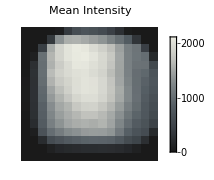
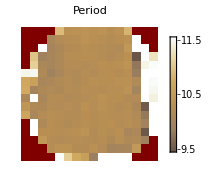

```mathematica
img=loadimage[basedir<>filename]; { Length[img], Length[img[[1]]], Length[img[[1,1]]] }
res=fitgrid[img,4,4,1,10.5];
plotres[res]
```

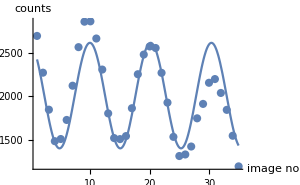
-Graphics- | Estimate | Standard Error | t-Statistic | P-Value
CameraIfgPackage`Private`a | 2009.36 | 39.1258 | 51.3565 | 1.45926×10^-31
CameraIfgPackage`Private`b | -611.303 | 55.9142 | -10.9329 | 3.65202×10^-12
CameraIfgPackage`Private`c | 0.613222 | 0.00864108 | 70.9659 | 7.01882×10^-36
CameraIfgPackage`Private`d | 1.77247 | 0.17306 | 10.2419 | 1.80525×10^-11contr=0.304227
offs=2009.36
phase=101.555°
period=10.2462

```mathematica
showtileres[res,8,8]
```

```mathematica
filename = "ifgPS2_3p_16Mar0112.tif";
```

{35,64,64}

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

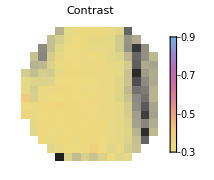
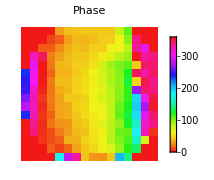
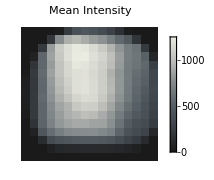
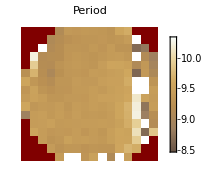

```mathematica
img=loadimage[basedir<>filename]; { Length[img], Length[img[[1]]], Length[img[[1,1]]] }
res=fitgrid[img,4,4,1,9.4];
plotres[res]
```

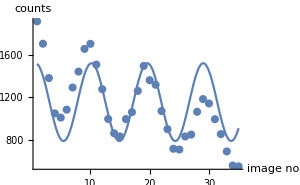
-Graphics- | Estimate | Standard Error | t-Statistic | P-Value
CameraIfgPackage`Private`a | 1156.07 | 38.8092 | 29.7884 | 2.23474×10^-24
CameraIfgPackage`Private`b | 366.498 | 53.9996 | 6.78705 | 1.33639×10^-7
CameraIfgPackage`Private`c | 0.666383 | 0.0154374 | 43.1668 | 2.96143×10^-29
CameraIfgPackage`Private`d | 1.07463 | 0.303275 | 3.5434 | 0.00127537contr=0.317022
offs=1156.07
phase=61.5715°
period=9.42879

```mathematica
showtileres[res,8,8]
```

```mathematica
filename = "ifgPS1_3p_16Mar0720.tif";
```

{28,64,64}

FittedModel::dof: The number of parameters 4 is not less than the number of data values 3. Some property values cannot be computed.

FittedModel::varzero: The estimated variance is zero. Properties requiring division by the variance or standard error will not be computed.

Part::partw: Part 2 of Missing[] does not exist.

Part::partw: Part 2 of If[Abs[Missing[] ⟦ 2, 1 ⟧] > 1, CameraIfgPackage`Private`result$189879, If[12 < 0, NonlinearModelFit[{0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0}, {CameraIfgPackage`Private`a + Abs[CameraIfgPackage`Private`b]\ Sin[Plus[« 2 »]]}, {« 1 »}, CameraIfgPackage`Private`x, AccuracyGoal → 5, Weights → (√#2 &)], NonlinearModelFit[{0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0}, CameraIfgPackage`Private`a + Abs[CameraIfgPackage`Private`b]\ Sin[Times[« 2 »] + CameraIfgPackage`Private`d], {{CameraIfgPackage`Private`a, Mean[{0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0}]}, {CameraIfgPackage`Private`b, 1/2\ (Max[« 1 »] + Times[« 2 »])}, {CameraIfgPackage`Private`c, 2\ π/12}, {CameraIfgPackage`Private`d, π}}, CameraIfgPackage`Private`x, AccuracyGoal → 5, Weights → (√#2 &)]]]["Para" … "tries"] does not exist.

Part::partd: Part specification « 1 » is longer than depth of object.

Part::partw: Part 2 of If[Abs[Missing[] ⟦ 2, 1 ⟧] > 1, CameraIfgPackage`Private`result$189879, If[12 < 0, NonlinearModelFit[{0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0}, {CameraIfgPackage`Private`a + Abs[CameraIfgPackage`Private`b]\ Sin[Plus[« 2 »]]}, {« 1 »}, CameraIfgPackage`Private`x, AccuracyGoal → 5, Weights → (√#2 &)], NonlinearModelFit[{0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0}, CameraIfgPackage`Private`a + Abs[CameraIfgPackage`Private`b]\ Sin[Times[« 2 »] + CameraIfgPackage`Private`d], {{CameraIfgPackage`Private`a, Mean[{0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0, 0, 1, 0, 0, 0, 0, 0}]}, {CameraIfgPackage`Private`b, 1/2\ (Max[« 1 »] + Times[« 2 »])}, {CameraIfgPackage`Private`c, 2\ π/12}, {CameraIfgPackage`Private`d, π}}, CameraIfgPackage`Private`x, AccuracyGoal → 5, Weights → (√#2 &)]]]["Para" … "tries"] does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Part::partd: Part specification « 1 » is longer than depth of object.

General::stop: Further output of Part :: partd will be suppressed during this calculation.

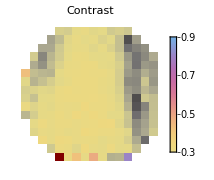
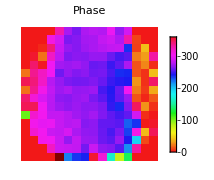
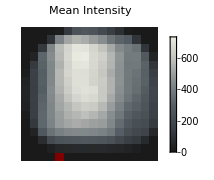
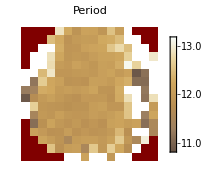

```mathematica
img=loadimage[basedir<>filename]; { Length[img], Length[img[[1]]], Length[img[[1,1]]] }
res=fitgrid[img,4,4,1,12];
plotres[res]
```

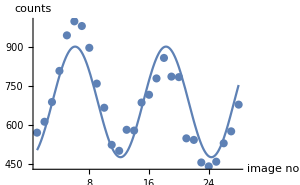
-Graphics- | Estimate | Standard Error | t-Statistic | P-Value
CameraIfgPackage`Private`a | 689.502 | 14.4323 | 47.7749 | 2.60996×10^-25
CameraIfgPackage`Private`b | 213.05 | 20.6972 | 10.2937 | 2.78451×10^-10
CameraIfgPackage`Private`c | 0.516192 | 0.0110457 | 46.7326 | 4.40756×10^-25
CameraIfgPackage`Private`d | -1.57632 | 0.185104 | -8.51587 | 1.02598×10^-8contr=0.308991
offs=689.502
phase=269.683°
period=12.1722

```mathematica
showtileres[res,8,8]
```